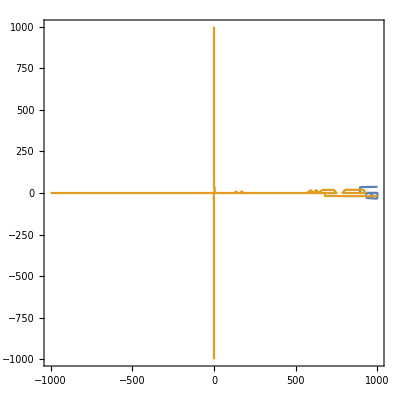

```mathematica
f=y*(9-x*y)*(x+2y-y^2)*((x-10)^2+(y-3)^2-1);
(*fx[y_,x_]:=(9-x*y)*(x+2y-y^2)*((x-10)^2+(y-3)^2-1)-(x*y)*(x+2y-y^2)*((x-10)^2+(y-3)^2-1)*)
(*ContourPlot[D[f,y]==0,{x,-1000,1000},{y,-1000,1000}]*)
fx=D[f,x];
fy=D[f,y];
ContourPlot[{fx==0,fy==0},{x,-1000,1000},{y,-1000,1000}]
```

```mathematica
FullSimplify[plot[(-1+(-10+x)^2+(-3+y)^2) y (9-x y)-(-1+(-10+x)^2+(-3+y)^2) y^2 (x+2 y-y^2)+2 (-10+x) y (9-x y) (x+2 y-y^2),{x,-1000,1000}]]
```

plot[y (972+9 x (-40+3 x)-414 y-4 x (45+(-15+x) x) y+(-27+74 x-6 x^2) y^2+3 (-10+x) (-4+x) y^3-8 y^4+y^5),{x,-1000,1000}]

```mathematica
g[x_,y_]:=y*(9-x*y)*(x+2y-y^2)*((x-10)^2+(y-3)^2-1);
g[20,-1]
```

-56695